## Cold alkali-atom multi-channel scattering with Mathematica

See the notes “ScatteringTheoryNotes-NPM-2019.nb” for an earlier version of this scattering code with the theory background.  See “LiPotentials.nb” for the background on the hyperfine and Zeeman matrix elements and projection operators. Here, I’m copying over the relevant modules to have a more compact notebook with only the code, and minimal exposition.

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μ=mLi7/2;
```

### Morse/Long-Range Potential For Lithium (Coded by A. Laskowski, See Le Roy et al)

```mathematica
ypeq[p_,r_]:= (r^p - 1^p)/(r^p +1^p);
ypref[p_,r_]:= (r^p - 1.5^p)/(r^p +1.5^p);
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DTT[r_,m_,btt_,ρ_,s_]:= 1-Exp[-btt ρ r]*Sum[(btt ρ r)^k/(k!),{k,0,m-1+s}];
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,0.54,-1];
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
t10 = 2.78683*10^9;
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
β[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

```mathematica
βinfT=βinf[tde,tre,DDSTriplet[6,tre],DDSTriplet[8,tre],DDSTriplet[10,tre],tc6,tc8,t10]
```

-0.509836

```mathematica
βTriplet[r_]:= βinfT*y[tref,r,5]+(1-y[tref,r,5])*Sum[tβcf[[j+1]]*y[tref,r,3]^j,{j,0,Length[tβcf]-1}];
ulrTriplet[r_]:= DDSTriplet[6,r] tc6/r^6+DDSTriplet[8,r] tc8/r^8+DDSTriplet[10,r] t10/r^10;
TripletMLR[r_]:= tde(1-ulrTriplet[r]/ulrTriplet[tre]*Exp[-βTriplet[r]*y[tre,r,p]])^2-tde;
```

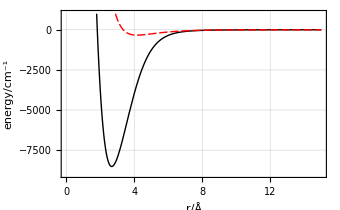

```mathematica
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
SingletMLR[r_]:= VMLR[r,sre,sde,β[r,sβcf1,βinf[sde,sre,1,1,1,C6,C8,C10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,C6,C8,C10]
Plot[{SingletMLR[r],TripletMLR[r]},{r,1.5,15},Frame->True,FrameLabel->{"r/Å","energy/cm^-1"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-9000,1000}]
```

#### Create an interpolated function to evaluate this fast

```mathematica
Rmax=80; (*bohr*)
Rmin=2.0;
NR =100;
dR=(Rmax-Rmin)/(NR-1);
RGrid =Table[Rmin+((iR-1)/(NR-1))^4(Rmax-Rmin),{iR,1,NR}];Length[RGrid]
```

100

```mathematica
TripletMLRHBdat = Table[{RGrid[[i]],invcminHartree*TripletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
TripletHBMLR=Interpolation[TripletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
SingletMLRHBdat = Table[{RGrid[[i]],invcminHartree*SingletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
SingletHBMLR=Interpolation[SingletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
```

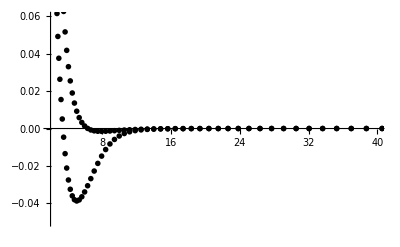

```mathematica
ListPlot[{SingletMLRHBdat,TripletMLRHBdat},PlotRange->{{Rmin,40},{-0.05,.06}}]
```

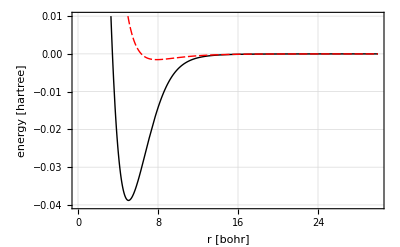

```mathematica
Plot[{SingletHBMLR[r],TripletHBMLR[r]},{r,Rmin,30},Frame->True,FrameLabel->{"r [bohr]","energy [hartree]"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-0.04,0.01}]
```

### Hyperfine & Zeeman Matrix Elements

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;
Li7AH =401.7520435*MHzPerHartree; (*MHz -> Hartree*)
Li6AH = 152.136840720*MHzPerHartree;  (*MHz -> Hartree*)
μbH = 1.3996244936142*MHzPerHartree;   (*MHz/G  ->  Hartree/G*)
μnH = 7.62259328547*10^-4*MHzPerHartree;(* MHz/G -> Hartree/G *)
```

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

For M_T=2

Unsymmetrized Basis

```mathematica
mF2unsym =Select[f1m1f2m2basis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

```mathematica
mF2basis = {{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,2,1}};
```

Use the following line and skip the lengthy projection operator calculation if you only want Li-7 M_F=2.

```mathematica
SymSingletProjLi7MF2={{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}};
SymTripletProjLi7MF2={{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}};
```

```mathematica
(*ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];*)

(*ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];*)
```

```mathematica
(*SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

```mathematica
(*SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]*)
```

```mathematica
(*SProjSymLi7=FullSimplify[SingletProjectionSym[0,0]]*)
```

{{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}}

```mathematica
(*MatrixForm[N[SProjSymLi7]]*)
```

(0.25 | -0.216506 | -0.176777 | -0.25 | 0.216506
-0.216506 | 0.1875 | 0.153093 | 0.216506 | -0.1875
-0.176777 | 0.153093 | 0.125 | 0.176777 | -0.153093
-0.25 | 0.216506 | 0.176777 | 0.25 | -0.216506
0.216506 | -0.1875 | -0.153093 | -0.216506 | 0.1875)

```mathematica
(*TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

For symmetrized basis:

```mathematica
(*TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]),{j,1,5},{jp,1,5}] *)
```

```mathematica
(*TProjSymLi7=FullSimplify[TripletProjectSym[0,0]];*)
```

```mathematica
(*TProjSymLi7*)
```

{{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}}

```mathematica
(*MatrixForm[N[TProjSymLi7]]*)
```

(0.75 | 0.216506 | 0.176777 | 0.25 | -0.216506
0.216506 | 0.8125 | -0.153093 | -0.216506 | 0.1875
0.176777 | -0.153093 | 0.875 | -0.176777 | 0.153093
0.25 | -0.216506 | -0.176777 | 0.75 | 0.216506
-0.216506 | 0.1875 | 0.153093 | 0.216506 | 0.8125)

(s i)f'm' H^HZ(s i)f m=A^HF/2[f(f+1)-s(s+1)-i(i+1)]δ_ff' δ_mm'+g_s μ_B B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_s(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'+g_i μ_N B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_i(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B √((2fp+1)(2f+1))Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B √((2fp+1)(2f+1))Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√((1+δ_αβ)(1+δ_α'β')))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
Eigensystem[FullSimplify[HZsym[0,0,B]]/.B->0][[1]]HartreePerMHz
```

{-1004.38,602.628,602.628,-200.876,-200.876}

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
```

```mathematica
Htest[r_,B_]:= HZsymLi7[B]+SymTripletProjLi7MF2*TripletHBMLR[r]+SymSingletProjLi7MF2*SingletHBMLR[r];
```

```mathematica
ValVecs[B_]:=Table[ Sort[Transpose[Eigensystem[Htest[RGrid [[iR]],B]]]],{iR,1,NR}];
```

```mathematica
AdiabaticUV=Table[{{RGrid[[iR]],ValVecs[0.0][[iR,n,1]]},ValVecs[0.0][[iR,n,2]]},{iR,1,NR},{n,1,5}];
```

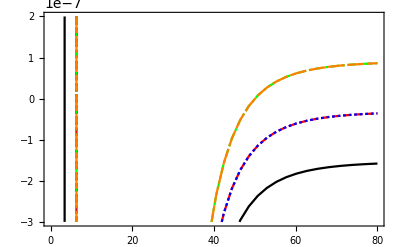

```mathematica
padiabatic=ListPlot[Table[AdiabaticUV[[1;;NR,n,1]],{n,1,5}],Joined->True,PlotMarkers->None,Frame->True,PlotRange->{-3 10^-7,2 10^-7},PlotStyle->{Black,Red,Blue,Green,Orange}]
```

```mathematica
Clear[Eth,AsymC];AsymC[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[2]];
Eth[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[1]];
```

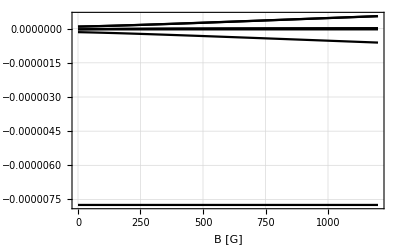

```mathematica
Plot[Flatten[{Eth[B],-7.739554008220906*^-6},1],{B,0,1200},PlotRange->All,Frame->True,GridLines->{Automatic},GridLinesStyle->Directive[Thin] ,FrameLabel->{"B [G]","Threshold Energies [Hartree]"}]
```

```mathematica
VR[r_,B_]:=AsymC[B]. HZsymLi7[B].Transpose[AsymC[B]]+AsymC[B].SymTripletProjLi7MF2.Transpose[AsymC[B]]*TripletHBMLR[r]+AsymC[B].SymSingletProjLi7MF2.Transpose[AsymC[B]]*SingletHBMLR[r];
```

```mathematica
Vmattest[r]=VR[r,0.0];
```

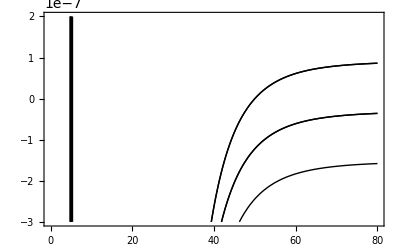

```mathematica
protated=Plot[Table[Vmattest[r][[n,n]],{n,1,5}],{r,Rmin,Rmax},PlotRange->{-3 10^-7,2 10^-7},Frame->True,PlotStyle->Thin]
```

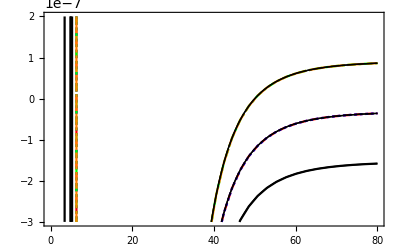

```mathematica
Show[{padiabatic,protated}]
```

### Scattering Asymptotic Functions

```mathematica
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
dse[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
dce[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

```mathematica
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
```

```mathematica
Nchan = 5;
Btest=0.0;
eps = 10^-15;
Etest=Eth[Btest][[1]]+eps
√(2μ(Etest-Eth[Btest][[1]]))
NumOpen[Energy_,B_]:=Count[Eth[B],u_/;u<Energy]
no = NumOpen[Etest,Btest]
```

-1.52649×10^-7

3.57623×10^-6

1

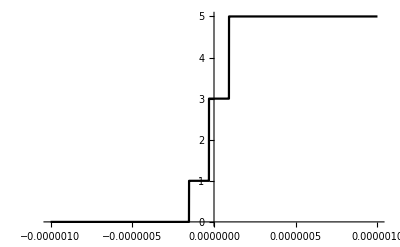

```mathematica
Plot[NumOpen[Energy,Btest],{Energy,-10^-6,10^-6}]
```

```mathematica
Nchan=5;Clear[α,β,u];
eqs[Ε_,r_,u_,Vmat_,Nchan_]:=Table[-1/(2μ)Subscript[u, i,α]''[r]+Sum[Vmat[r][[i,j]]Subscript[u, j,α][r],{j,1,Nchan}]-Ε Subscript[u, i,α][r]==0,{i,1,Nchan},{α,1,Nchan}];
boundarycond[Ε_,rmin_,rmax_,Eth_,Nchan_,u_]:=Module[{},
Table[{
Subscript[u, ii,β][rmin]==0,
With[{i=ii,α=β},If[Ε<Eth[[i]],
Subscript[u, i,α][rmax]==0,
Subscript[u, i,α]'[rmin]==KroneckerDelta[i,α]]]},
{ii,1,Nchan},{β,1,Nchan}]
];
(*boundarycond[Ε_,rmin_,rmax_,Eth_,Nchan_,u_]:=Module[{},
Table[{
Subscript[u, ii,β][rmin]==0,
With[{i=ii,α=β},
Subscript[u, i,α]'[rmin]==10^-5 KroneckerDelta[i,α]]
(*If[Ε<Eth[[i]],
Subscript[u, i,α][rmax]==0,
Subscript[u, i,α]'[rmin]==10^-5 KroneckerDelta[i,α]]]*);
},
{ii,1,Nchan},{β,1,Nchan}]
];*)
alleqs[Ε_,r_,rmin_,rmax_,Eth_,Nchan_,u_,Vmat_]:=Table[Flatten[{Transpose[eqs[Ε,r,u,Vmat,Nchan]][[i]],Transpose[boundarycond[Ε,rmin,rmax,Eth,Nchan,u]][[i]]}],{i,1,Nchan}];
```

```mathematica
diagsc=Setupdiagsc[Etest,no,Eth[Btest],r,μ];
```

```mathematica
VV[r]=VR[r,Btest];
Clear[umat,u];
umat=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,1,Nchan}];
equations=alleqs[Etest,r,Rmin,Rmax,Eth[Btest],Nchan,u,VV];
sol=NDSolve[equations,umatᵀ,{r,Rmin,Rmax},Method->{"Automatic"}]
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 2.07915×10^41 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{{u_(1,1)[r],u_(2,1)[r],u_(3,1)[r],u_(4,1)[r],u_(5,1)[r]}→{InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]},{u_(1,2)[r],u_(2,2)[r],u_(3,2)[r],u_(4,2)[r],u_(5,2)[r]}→{InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]},{u_(1,3)[r],u_(2,3)[r],u_(3,3)[r],u_(4,3)[r],u_(5,3)[r]}→{InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]},{u_(1,4)[r],u_(2,4)[r],u_(3,4)[r],u_(4,4)[r],u_(5,4)[r]}→{InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]},{u_(1,5)[r],u_(2,5)[r],u_(3,5)[r],u_(4,5)[r],u_(5,5)[r]}→{InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r],InterpolatingFunction[…][r]}}}

```mathematica
umat/.sol/.r->Rmax
```

{{{u_(1,1)[80],u_(1,2)[80],u_(1,3)[80],u_(1,4)[80],u_(1,5)[80]},{u_(2,1)[80],u_(2,2)[80],u_(2,3)[80],u_(2,4)[80],u_(2,5)[80]},{u_(3,1)[80],u_(3,2)[80],u_(3,3)[80],u_(3,4)[80],u_(3,5)[80]},{u_(4,1)[80],u_(4,2)[80],u_(4,3)[80],u_(4,4)[80],u_(4,5)[80]},{u_(5,1)[80],u_(5,2)[80],u_(5,3)[80],u_(5,4)[80],u_(5,5)[80]}}}

```mathematica
Unprotect[Kmatrix];Kmatrix[Eth_,nchan_,no_,r_,rmin_,rmax_,Vmat_,Ε_]:=Module[{K,Imat,Jmat,sols,eqs,uopen,umat,u,i,j,α,β,diagsc,S},
diagsc=Setupdiagsc[Ε,no,Eth,r];
umat=Table[Subscript[u, i,j][r],{i,1,nchan},{j,1,nchan}];
eqs=alleqs[Ε,r,rmin,rmax,Eth,nchan,u,Vmat];
sols=Flatten[Table[NDSolve[eqs[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,nchan}]];
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
Imat=Table[Wronskian[{uopen[[i,β]],diagsc[[2,i,i]]},r]/Wronskian[{diagsc[[1,i,i]],diagsc[[2,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;Jmat=Table[Wronskian[{uopen[[i,β]],diagsc[[1,i,i]]},r]/Wronskian[{diagsc[[2,i,i]],diagsc[[1,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;
K=Jmat.Inverse[Imat]/.r->rmax;
S=(IdentityMatrix[no]+ⅈ K).Inverse[IdentityMatrix[no]-ⅈ K];
{K,S}
]
Protect[Kmatrix];
```

```mathematica
Kmatrix[Eth[Btest],Nchan,no,r,Rmin,Rmax,VV,Etest]
```

DiagonalMatrix::vector: Argument {{0.182715 r SphericalBesselJ[0,0.104881 r]}} at position 1 is not a non-empty vector.

DiagonalMatrix::vector: Argument {{-0.182715 r SphericalBesselY[0,0.104881 r]}} at position 1 is not a non-empty vector.

DiagonalMatrix::vector: Argument {{0.00958163 r SphericalBesselJ[-1,0.104881 r]+0.0913573 SphericalBesselJ[0,«1»]-0.00958163 r SphericalBesselJ[1,0.104881 r]}} at position 1 is not a non-empty vector.

General::stop: Further output of DiagonalMatrix::vector will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80.5278} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 1.00797×10^41 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

General::stop: Further output of NDSolve::bvluc will be suppressed during this calculation.

$Aborted

```mathematica
dat=Table[{Eth[Btest][[1]]+eps,Kmatrix[Eth[Btest],Nchan,no,r,Rmin,Rmax,VV/.{VV[r]->VR[r,Btest]},Eth[Btest][[1]]+eps]},{Btest,0,1000,20}];
```

DiagonalMatrix::vector: Argument {{0.182715 r SphericalBesselJ[0,0.104881 r]}} at position 1 is not a non-empty vector.

DiagonalMatrix::vector: Argument {{-0.182715 r SphericalBesselY[0,0.104881 r]}} at position 1 is not a non-empty vector.

DiagonalMatrix::vector: Argument {{0.00958163 r SphericalBesselJ[-1,0.104881 r]+0.0913573 SphericalBesselJ[0,«1»]-0.00958163 r SphericalBesselJ[1,0.104881 r]}} at position 1 is not a non-empty vector.

General::stop: Further output of DiagonalMatrix::vector will be suppressed during this calculation.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 7.09269×10^40 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

General::stop: Further output of NDSolve::bvluc will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 8.66189×10^40 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 5.79367×10^40 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

```mathematica
Li7FRData=Import["/Users/niravmehta/Documents/GitHub/LiScattering/Li7-FR-ScatLen.dat"];
```

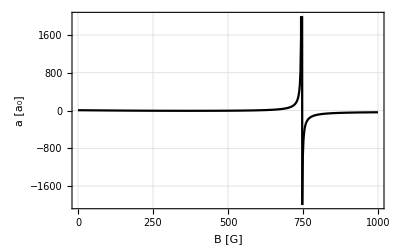

```mathematica
ListPlot[Li7FRData,Joined->True,PlotMarkers->None,Frame->True,PlotRange->{-2000,2000},FrameLabel->{"B [G]","a [a_0]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin]
```

### QDT

```mathematica
SymSingletProjLi7MF2={{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}};
SymTripletProjLi7MF2={{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}};
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B √((2fp+1)(2f+1))Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B √((2fp+1)(2f+1))Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√((1+δ_αβ)(1+δ_α'β')))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
```

```mathematica
Clear[Eth,AsymC];AsymC[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[2]];
Eth[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[1]];
```

```mathematica
μdefect[s_]:=Which[s==0,-0.00872,s==1,0.07484]
```

```mathematica
KSRhf=Sum[SymSingletProjLi7MF2*Tan[π μdefect[0]] + SymTripletProjLi7MF2*Tan[π μdefect[1]]3(2 itot+1),{itot,0,2Li7i}]
```

{{8.5963,2.51318,2.052,2.90197,-2.51318},{2.51318,9.32179,-1.77709,-2.51318,2.17648},{2.052,-1.77709,10.0473,-2.052,1.77709},{2.90197,-2.51318,-2.052,8.5963,2.51318},{-2.51318,2.17648,1.77709,2.51318,9.32179}}